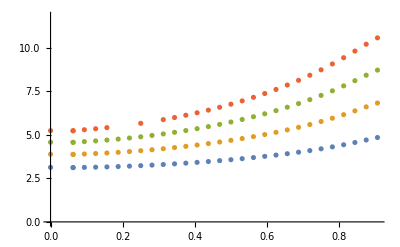

```mathematica
a={{0,3.130919},{0.062500,3.118583},{0.062500,3.118583},{0.093750,3.128569},{0.125000,3.140804},{0.156250,3.157232},{0.187500,3.177726},{0.218750,3.202008},{0.250000,3.229841},{0.281250,3.261050},{0.312500,3.295530},{0.343750,3.333230},{0.375000,3.374158},{0.406250,3.418376},{0.437500,3.465994},{0.468750,3.517178},{0.500000,3.572145},{0.531250,3.631171},{0.562500,3.694593},{0.593750,3.762816},{0.625000,3.836326},{0.656250,3.915695},{0.687500,4.001601},{0.718750,4.094843},{0.750000,4.196346},{0.781250,4.307149},{0.812500,4.428290},{0.843750,4.560383},{0.875000,4.702090},{0.906250,4.844211}};
a2={{0,3.883919},{0.062500,3.873624},{0.062500,3.873624},{0.093750,3.899067},{0.125000,3.925200},{0.156250,3.956988},{0.187500,3.994756},{0.218750,4.038323},{0.250000,4.087486},{0.281250,4.142106},{0.312500,4.202131},{0.343750,4.267588},{0.375000,4.338587},{0.406250,4.415310},{0.437500,4.498014},{0.468750,4.587026},{0.500000,4.682747},{0.531250,4.785647},{0.562500,4.896279},{0.593750,5.015274},{0.625000,5.143356},{0.656250,5.281348},{0.687500,5.430188},{0.718750,5.590935},{0.750000,5.764761},{0.781250,5.952885},{0.812500,6.156301},{0.843750,6.374839},{0.875000,6.603836},{0.906250,6.823195}};
a3={{0,4.575125},{0.062500,4.567850},{0.062500,4.567850},{0.093750,4.609620},{0.125000,4.650274},{0.156250,4.697861},{0.187500,4.753201},{0.218750,4.816247},{0.250000,4.886855},{0.281250,4.964939},{0.312500,5.050510},{0.343750,5.143678},{0.375000,5.244651},{0.406250,5.353731},{0.437500,5.471309},{0.468750,5.597866},{0.500000,5.733964},{0.531250,5.880254},{0.562500,6.037473},{0.593750,6.206446},{0.625000,6.388096},{0.656250,6.583450},{0.687500,6.793650},{0.718750,7.019950},{0.750000,7.263700},{0.781250,7.526228},{0.812500,7.808436},{0.843750,8.109431},{0.875000,8.421596},{0.906250,8.714422}};
a4={{0,5.238260},{0.062500,5.234179},{0.062500,5.234179},{0.093750,5.292505},{0.125000,5.347859},{0.156250,5.411392},{0.187500,29.776953},{0.218750,27.780364},{0.250000,5.659143},{0.281250,27.771327},{0.312500,5.871897},{0.343750,5.992808},{0.375000,6.123783},{0.406250,6.265240},{0.437500,6.417702},{0.468750,6.581795},{0.500000,6.758237},{0.531250,6.947843},{0.562500,7.151518},{0.593750,7.370261},{0.625000,7.605168},{0.656250,7.857437},{0.687500,8.128374},{0.718750,8.419387},{0.750000,8.731954},{0.781250,9.067461},{0.812500,9.426686},{0.843750,9.808032},{0.875000,10.201205},{0.906250,10.566154}};
ListPlot[{a,a2,a3,a4}]
```

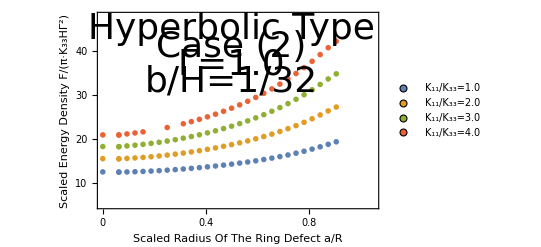

```mathematica
aa=a*Table[{1,4},{i,0,29}];
aa2=a2*Table[{1,4},{i,0,29}];
aa3=a3*Table[{1,4},{i,0,29}];
aa4=a4*Table[{1,4},{i,0,29}];
ListPlot[{aa,aa2,aa3,aa4},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{10,20,30,40},None},{{0,0.2, 0.4, 0.6, 0.8,1.0},None}}, PlotRange->{{0,1.05},{5,48}},FrameLabel->{{"Scaled Energy Density F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=1.0","K_11/K_33=2.0","K_11/K_33=3.0","K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Hyperbolic Type",Directive[Black,36]],{0.5,45}],Text[Style["Case (2)",Directive[Black,36]],{0.5,41}],Text[Style["Γ=1.0",Directive[Black,36]],{0.5,37}],Text[Style["b/H=1/32",Directive[Black,36]],{0.5,33}]}]
```